```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues/gpls/positive"];
ViewSurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
plot1=ListPlot3D[data,BoxRatios->Automatic];
plot2=ListPlot[Transpose[Drop[Transpose[data],-1]], PlotRange->{{ 0, 500}, {-500, 500}}];
{plot1,plot2}
]
files= FileNames[];
numbersInString[s_]:=ToExpression@StringCases[s,NumberString]
files = SortBy[files,numbersInString]
allPlots=Table[ViewSurface[file],{file,files}];
(*ListAnimate[allPlots]*)
```

{surface0positive.gpl,surface1positive.gpl,surface2positive.gpl,surface3positive.gpl,surface4positive.gpl,surface5positive.gpl,surface6positive.gpl,surface7positive.gpl,surface8positive.gpl,surface9positive.gpl,surface10positive.gpl,surface11positive.gpl,surface12positive.gpl,surface13positive.gpl,surface14positive.gpl,surface15positive.gpl,surface16positive.gpl,surface17positive.gpl,surface18positive.gpl,surface19positive.gpl,surface20positive.gpl,surface21positive.gpl,surface22positive.gpl,surface23positive.gpl,surface24positive.gpl,surface25positive.gpl,surface26positive.gpl,surface27positive.gpl,surface28positive.gpl,surface29positive.gpl,surface30positive.gpl,surface31positive.gpl,surface32positive.gpl,surface33positive.gpl,surface34positive.gpl,surface35positive.gpl,surface36positive.gpl,surface37positive.gpl,surface38positive.gpl,surface39positive.gpl,surface40positive.gpl,surface41positive.gpl,surface42positive.gpl,surface43positive.gpl,surface44positive.gpl,surface45positive.gpl,surface46positive.gpl,surface47positive.gpl,surface48positive.gpl,surface49positive.gpl,surface50positive.gpl,surface51positive.gpl,surface52positive.gpl,surface53positive.gpl,surface54positive.gpl,surface55positive.gpl,surface56positive.gpl,surface57positive.gpl,surface58positive.gpl,surface59positive.gpl,surface60positive.gpl,surface61positive.gpl,surface62positive.gpl,surface63positive.gpl,surface64positive.gpl,surface65positive.gpl,surface66positive.gpl,surface67positive.gpl,surface68positive.gpl,surface69positive.gpl,surface70positive.gpl,surface71positive.gpl,surface72positive.gpl,surface73positive.gpl,surface74positive.gpl,surface75positive.gpl,surface76positive.gpl,surface77positive.gpl,surface78positive.gpl,surface79positive.gpl,surface80positive.gpl,surface81positive.gpl,surface82positive.gpl,surface83positive.gpl,surface84positive.gpl,surface85positive.gpl,surface86positive.gpl,surface87positive.gpl,surface88positive.gpl,surface89positive.gpl,surface90positive.gpl,surface91positive.gpl,surface92positive.gpl,surface93positive.gpl,surface94positive.gpl,surface95positive.gpl,surface96positive.gpl,surface97positive.gpl,surface98positive.gpl,surface99positive.gpl,surface100positive.gpl,surface101positive.gpl,surface102positive.gpl,surface103positive.gpl,surface104positive.gpl,surface105positive.gpl,surface106positive.gpl,surface107positive.gpl,surface108positive.gpl,surface109positive.gpl,surface110positive.gpl,surface111positive.gpl,surface112positive.gpl,surface113positive.gpl,surface114positive.gpl,surface115positive.gpl,surface116positive.gpl,surface117positive.gpl,surface118positive.gpl,surface119positive.gpl,surface120positive.gpl,surface121positive.gpl,surface122positive.gpl,surface123positive.gpl,surface124positive.gpl,surface125positive.gpl,surface126positive.gpl,surface127positive.gpl,surface128positive.gpl,surface129positive.gpl,surface130positive.gpl,surface131positive.gpl,surface132positive.gpl,surface133positive.gpl,surface134positive.gpl,surface135positive.gpl,surface136positive.gpl,surface137positive.gpl,surface138positive.gpl,surface139positive.gpl,surface140positive.gpl,surface141positive.gpl,surface142positive.gpl,surface143positive.gpl,surface144positive.gpl,surface145positive.gpl,surface146positive.gpl,surface147positive.gpl,surface148positive.gpl,surface149positive.gpl,surface150positive.gpl,surface151positive.gpl,surface152positive.gpl,surface153positive.gpl,surface154positive.gpl,surface155positive.gpl,surface156positive.gpl,surface157positive.gpl,surface158positive.gpl,surface159positive.gpl,surface160positive.gpl,surface161positive.gpl,surface162positive.gpl,surface163positive.gpl,surface164positive.gpl,surface165positive.gpl,surface166positive.gpl,surface167positive.gpl,surface168positive.gpl,surface169positive.gpl,surface170positive.gpl}

{{50,6.59752×10^6},{60,6.70226×10^6},{70,6.6841×10^6},{80,6.62062×10^6},{90,6.53972×10^6},{100,6.45258×10^6},{110,6.36396×10^6},{120,6.27599×10^6},{130,6.18966×10^6},{140,6.10543×10^6},{150,6.02352×10^6},{160,5.94401×10^6},{170,5.86694×10^6},{180,5.79231×10^6},{190,5.72015×10^6},{200,5.65083×10^6},{210,5.56642×10^6},{220,5.51418×10^6},{230,5.4511×10^6},{240,5.38962×10^6},{250,5.32997×10^6},{260,5.27217×10^6},{270,5.21615×10^6},{280,5.16188×10^6},{290,5.10929×10^6},{300,5.05833×10^6},{310,5.00894×10^6},{320,4.96107×10^6},{330,4.91467×10^6},{340,4.86968×10^6},{350,4.82605×10^6},{360,4.78374×10^6},{370,4.74271×10^6},{380,4.70289×10^6},{390,4.66426×10^6},{400,4.62678×10^6},{410,4.59039×10^6},{420,4.55508×10^6},{430,4.52079×10^6},{440,4.4875×10^6},{450,4.45517×10^6},{460,4.42376×10^6},{470,4.39326×10^6},{480,4.36362×10^6},{490,4.33483×10^6},{500,4.30684×10^6},{510,4.27964×10^6},{520,4.2532×10^6},{530,4.2275×10^6},{540,4.20251×10^6},{550,4.17821×10^6},{560,4.15457×10^6},{570,4.13158×10^6},{580,4.10921×10^6},{590,4.08745×10^6},{600,4.06627×10^6},{610,4.04566×10^6},{620,4.0256×10^6},{630,4.00606×10^6},{640,3.98705×10^6},{650,3.96853×10^6},{660,3.95049×10^6},{670,3.93292×10^6},{680,3.9158×10^6},{690,3.89912×10^6},{700,3.88286×10^6},{710,3.86701×10^6},{720,3.85155×10^6},{730,3.83648×10^6},{740,3.82178×10^6},{750,3.80744×10^6},{760,3.79344×10^6},{770,3.77978×10^6},{780,3.76644×10^6},{790,3.75341×10^6},{800,3.74068×10^6},{810,3.72825×10^6},{820,3.71609×10^6},{830,3.7042×10^6},{840,3.69258×10^6},{850,3.6812×10^6},{860,3.67007×10^6},{870,3.65916×10^6},{880,3.64848×10^6},{890,3.63801×10^6},{900,3.62775×10^6},{910,3.61768×10^6},{920,3.60779×10^6},{930,3.59809×10^6},{940,3.58856×10^6},{950,3.57919×10^6},{960,3.56997×10^6},{970,3.5609×10^6},{980,3.55196×10^6},{990,3.54316×10^6},{1000,3.53447×10^6},{1010,3.52591×10^6},{1020,3.51744×10^6},{1030,3.50908×10^6},{1040,3.50081×10^6},{1050,3.49262×10^6},{1060,3.48451×10^6},{1070,3.47647×10^6},{1080,3.46849×10^6},{1090,3.46056×10^6},{1100,3.45268×10^6},{1110,3.44484×10^6},{1120,3.43703×10^6},{1130,3.42924×10^6},{1140,3.42147×10^6},{1150,3.4137×10^6},{1160,3.40594×10^6},{1170,3.39817×10^6},{1180,3.39038×10^6},{1190,3.38257×10^6},{1200,3.37473×10^6},{1210,3.36685×10^6},{1220,3.35892×10^6},{1230,3.35093×10^6},{1240,3.34288×10^6},{1250,3.33475×10^6},{1260,3.32655×10^6},{1270,3.31825×10^6},{1280,3.30985×10^6},{1290,3.30134×10^6},{1300,3.29271×10^6},{1310,3.28395×10^6},{1320,3.27505×10^6},{1330,3.266×10^6},{1340,3.25679×10^6},{1350,3.24741×10^6},{1360,3.23785×10^6},{1370,3.22809×10^6},{1380,3.21812×10^6},{1390,3.20794×10^6},{1400,3.19752×10^6},{1410,3.18686×10^6},{1420,3.17594×10^6},{1430,3.16474×10^6},{1440,3.15326×10^6},{1450,3.14147×10^6},{1460,3.12936×10^6},{1470,3.11692×10^6},{1480,3.10412×10^6},{1490,3.09095×10^6},{1500,3.07738×10^6},{1510,3.0634×10^6},{1520,3.04899×10^6},{1530,3.03412×10^6},{1540,3.01877×10^6},{1550,3.00291×10^6},{1560,2.98652×10^6},{1570,2.96957×10^6},{1580,2.95203×10^6},{1590,2.93386×10^6},{1600,2.91504×10^6},{1610,2.89552×10^6},{1620,2.87526×10^6},{1630,2.85423×10^6},{1640,2.83238×10^6},{1650,2.80965×10^6},{1660,2.78599×10^6},{1670,2.76135×10^6},{1680,2.73566×10^6},{1690,2.70884×10^6},{1700,2.68083×10^6},{1710,2.65153×10^6},{1720,2.62085×10^6},{1730,2.58867×10^6},{1740,2.55488×10^6},{1750,2.51933×10^6}}

{{50,65.9752},{60,67.0226},{70,66.841},{80,66.2062},{90,65.3972},{100,64.5258},{110,63.6396},{120,62.7599},{130,61.8966},{140,61.0543},{150,60.2352},{160,59.4401},{170,58.6694},{180,57.9231},{190,57.2015},{200,56.5083},{210,55.6642},{220,55.1418},{230,54.511},{240,53.8962},{250,53.2997},{260,52.7217},{270,52.1615},{280,51.6188},{290,51.0929},{300,50.5833},{310,50.0894},{320,49.6107},{330,49.1467},{340,48.6968},{350,48.2605},{360,47.8374},{370,47.4271},{380,47.0289},{390,46.6426},{400,46.2678},{410,45.9039},{420,45.5508},{430,45.2079},{440,44.875},{450,44.5517},{460,44.2376},{470,43.9326},{480,43.6362},{490,43.3483},{500,43.0684},{510,42.7964},{520,42.532},{530,42.275},{540,42.0251},{550,41.7821},{560,41.5457},{570,41.3158},{580,41.0921},{590,40.8745},{600,40.6627},{610,40.4566},{620,40.256},{630,40.0606},{640,39.8705},{650,39.6853},{660,39.5049},{670,39.3292},{680,39.158},{690,38.9912},{700,38.8286},{710,38.6701},{720,38.5155},{730,38.3648},{740,38.2178},{750,38.0744},{760,37.9344},{770,37.7978},{780,37.6644},{790,37.5341},{800,37.4068},{810,37.2825},{820,37.1609},{830,37.042},{840,36.9258},{850,36.812},{860,36.7007},{870,36.5916},{880,36.4848},{890,36.3801},{900,36.2775},{910,36.1768},{920,36.0779},{930,35.9809},{940,35.8856},{950,35.7919},{960,35.6997},{970,35.609},{980,35.5196},{990,35.4316},{1000,35.3447},{1010,35.2591},{1020,35.1744},{1030,35.0908},{1040,35.0081},{1050,34.9262},{1060,34.8451},{1070,34.7647},{1080,34.6849},{1090,34.6056},{1100,34.5268},{1110,34.4484},{1120,34.3703},{1130,34.2924},{1140,34.2147},{1150,34.137},{1160,34.0594},{1170,33.9817},{1180,33.9038},{1190,33.8257},{1200,33.7473},{1210,33.6685},{1220,33.5892},{1230,33.5093},{1240,33.4288},{1250,33.3475},{1260,33.2655},{1270,33.1825},{1280,33.0985},{1290,33.0134},{1300,32.9271},{1310,32.8395},{1320,32.7505},{1330,32.66},{1340,32.5679},{1350,32.4741},{1360,32.3785},{1370,32.2809},{1380,32.1812},{1390,32.0794},{1400,31.9752},{1410,31.8686},{1420,31.7594},{1430,31.6474},{1440,31.5326},{1450,31.4147},{1460,31.2936},{1470,31.1692},{1480,31.0412},{1490,30.9095},{1500,30.7738},{1510,30.634},{1520,30.4899},{1530,30.3412},{1540,30.1877},{1550,30.0291},{1560,29.8652},{1570,29.6957},{1580,29.5203},{1590,29.3386},{1600,29.1504},{1610,28.9552},{1620,28.7526},{1630,28.5423},{1640,28.3238},{1650,28.0965},{1660,27.8599},{1670,27.6135},{1680,27.3566},{1690,27.0884},{1700,26.8083},{1710,26.5153},{1720,26.2085},{1730,25.8867},{1740,25.5488},{1750,25.1933}}

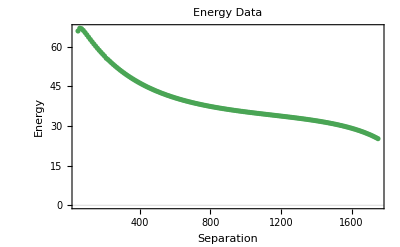

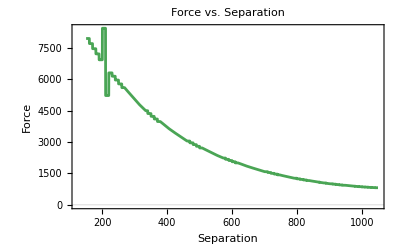

```mathematica
SolveForce[filename_] :=
Module[{stream, data,force, forcefunction, forceplot, x},
stream = OpenRead[filename];
data = ReadList[stream,{Number,Number}];
Close[stream];
data
];
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues"];
Print[SolveForce["energysep.txt"]];
allData=SolveForce["energysep.txt"];
{sep, energy}= Transpose[allData];
showData = Transpose[{sep,Map[#/(10^5)&,energy//N]}]
energyGraph = ListPlot[showData, PlotRange->All, PlotLabel->"Energy Data", PlotTheme->"Scientific", AxesLabel->{"Separation", "Energy"}, PlotStyle->Darker[Blend[{Green, LightBlue}]]]
(*ListPlot[allData,Joined->True]*)
force[x_]=-D[Interpolation[allData,InterpolationOrder->1][x],x];
forceGraph = Plot[force[x],{x,150, 1050},PlotTheme->"Scientific", AxesLabel->{"Separation", "Force"}, AxesOrigin->{125,-15}, PlotLabel->"Force vs. Separation", PlotStyle->{{Thickness[0.005],Darker[Blend[{Green, LightBlue}]]}}]
SetDirectory[StringJoin[NotebookDirectory[],"gpls/"]];
```

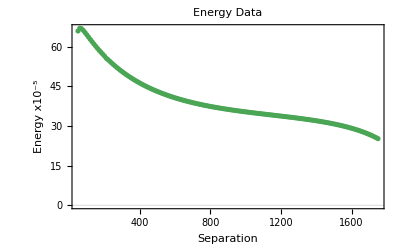

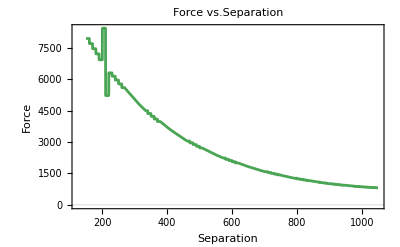

```mathematica
energyGraphnice = Show[energyGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Energy x10^("-5")],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Energy Data],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full]
forceGraphnice = Show[forceGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Force],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Force vs. Separation],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full]
```

```mathematica
Close[stream];
```

```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues/gpls/positive"];
prettySurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["DarkRainbow"];
prettyData=ListPlot3D[data,Mesh->20, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->{Automatic,Automatic,100}, PlotStyle->Opacity[.9], Boxed->False, Axes->False, Background->None];
prettyData
]
prettySurface["surface40positive.gpl"]
```

-Graphics3D-

```mathematica
prettySurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["DarkRainbow"];
prettyData=ListPlot3D[data,Mesh->10, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->Automatic, PlotStyle->Opacity[.9], Boxed->False, Axes->False, Background->None,PlotRange->{{-300,300},{-150,150},Automatic}];
Show[prettyData,Graphics3D[{Black,Sphere[{137.5,0,400},10],Cylinder[{{-137.5,0,399},{-137.5,0,401}},10]}]]
]
prettySurface["surface40positive.gpl"]
```

-Graphics3D-

```mathematica
|
```